```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY189/morning_sec_int_data/412nm.dat"]
```

{{1.12389,-0.00920221},{1.13423,0.00169856},{1.14739,-0.00144104},{1.16401,-0.011688},{1.183,-0.000520135},{1.20042,-0.0168105},{1.22646,-0.0217345},{1.24828,-0.0298099},{1.27782,-0.0471231},{1.30453,-0.0587208},{1.34407,-0.0647412},{1.38078,-0.0889952},{1.41705,-0.105449},{1.46132,-0.122993},{1.51023,-0.148245},{1.58758,-0.183466},{1.63065,-0.196489}}

0.4645-0.402934 x

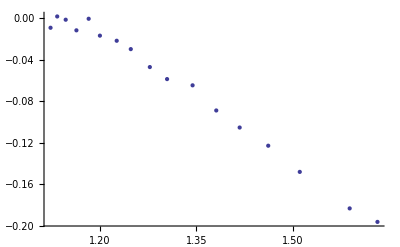

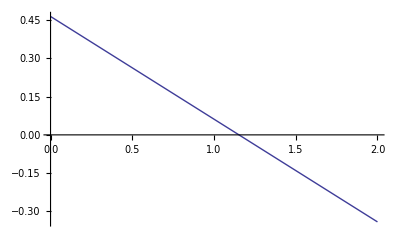

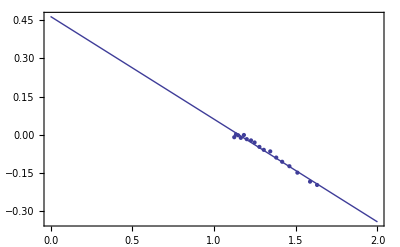

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```